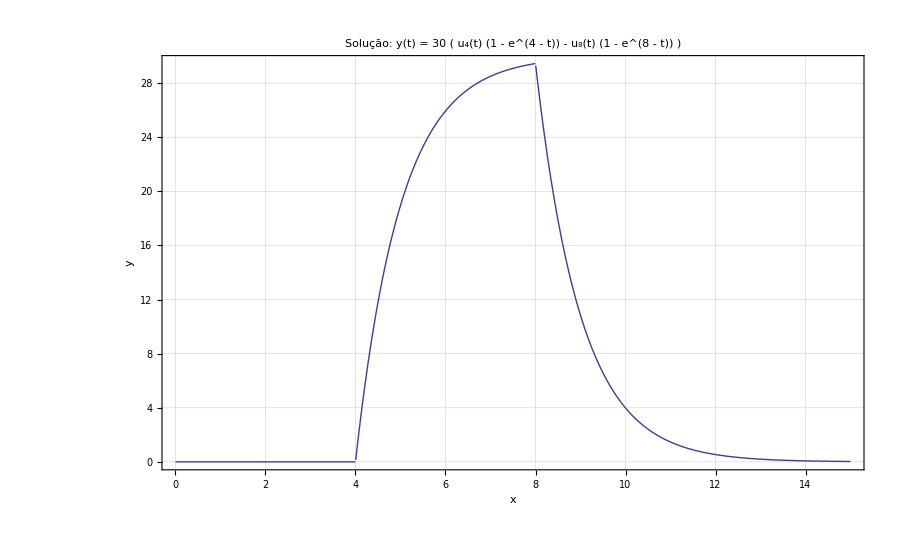

```mathematica
Plot[-30 Exp[-x]((Exp[x]-Exp[8]) UnitStep[x-8]-(Exp[x]-Exp[4]) UnitStep[x-4]),{x,0,15},PlotRange->All,ImageSize->900,AxesLabel->{"x","y"},AxesStyle->Directive[15],PlotStyle->Thick,GridLines->Automatic, GridLinesStyle->Directive[Black,Dashed],Frame->True,PlotLabel->Style["Solução:  y(t) = 30 ( u_4(t) (1 - e^(4 - t)) - u_8(t) (1 - e^(8 - t)) )",20]]
```

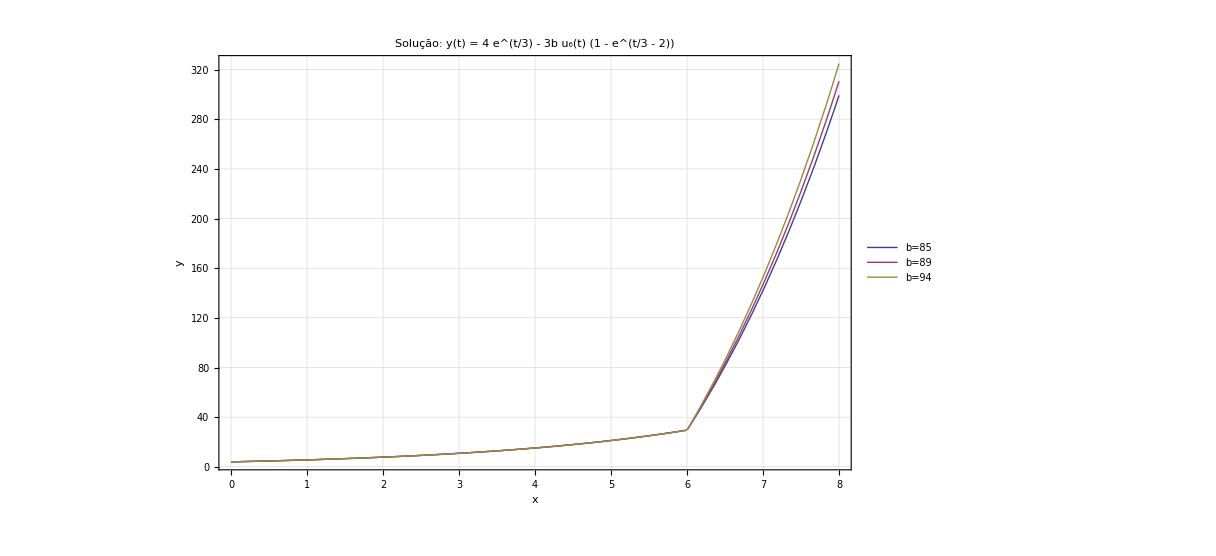

```mathematica
Plot[{
4 Exp[x/3]-3*85 UnitStep[x-6](1-Exp[x/3-2]),
4 Exp[x/3]-3*89 UnitStep[x-6](1-Exp[x/3-2]),
4 Exp[x/3]-3*94 UnitStep[x-6](1-Exp[x/3-2])
},{x,0,8},PlotRange->All,ImageSize->900,AxesLabel->{"x","y"},AxesStyle->Directive[15],PlotStyle->Thick,GridLines->Automatic, GridLinesStyle->Directive[Black,Dashed],Frame->True,PlotLegends->{"b=85","b=89","b=94"},PlotLabel->Style["Solução:  y(t) = 4 e^(t/3) - 3b u_6(t) (1 - e^(t/3 - 2)) ",20]]
```

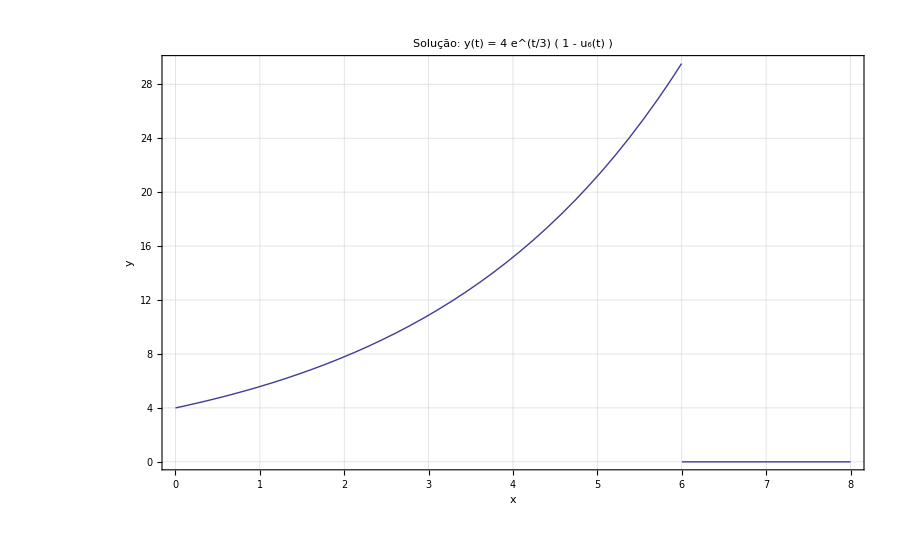

```mathematica
Plot[4 Exp[x/3](1-UnitStep[x-6]),{x,0,8},PlotRange->All,ImageSize->900,AxesLabel->{"x","y"},AxesStyle->Directive[15],PlotStyle->Thick,GridLines->Automatic, GridLinesStyle->Directive[Black,Dashed],Frame->True,PlotLabel->Style["Solução:  y(t) = 4 e^(t/3) ( 1 - u_6(t) )",20]]
```